## Analytic Solutions to the Mapping functions

We need to define numeric values for all the variables present

```mathematica
rss:=l^2/rH  ArcCoth[-rS/rH];
 ϵ=0.01; l=0.5*10^(1/4);
 Temp=0.5;x0=0;
l0=4;
T=2/Pi;
rH=(4 Pi l^2Temp)/(d-1) /. d-> 3;
rS=(1+ϵ)rH;
```

In order to see the printed results in terms of the variables and not their values, these variables may optionally be cleared:

```mathematica
Clear[rss,l,Temp,T,l0,rH,ϵ]
```

Though the above cell defining them must then be re-run before any numeric calculations are performed.

Defining the square parameter space and its minimal partitioning as define in section (2.2)

```mathematica
M[σF_] := ImplicitRegion[0<= t<= σF && 0<= s <= σF, {t,s}];
M1[σF_] := ImplicitRegion[0<= t<= σF && 0<= s <= σF-t, {t,s}];
M2[σF_] := ImplicitRegion[0<= t<= σF && σF-t< s <= σF, {t,s}];
```

Plots showing the parameter space and this partitioning, for the case of σ_f=4:

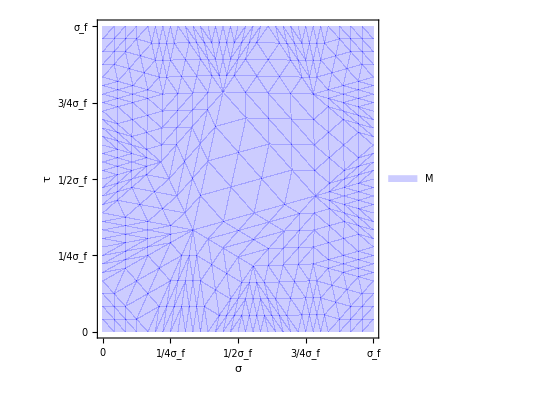

-Graphics-

```mathematica
WSPlot[M_,leg_]:=RegionPlot[M,PlotLegends->leg,BoundaryStyle -> None,PlotStyle->{{Opacity[0.2,Blue]},{Opacity[0.2,Red]}},FrameLabel->{Style[σ,Bold,13] ,Style[τ,Bold,13]},FrameTicks->{{{{0,0} ,{1,"1/4σ_f"},{2,"1/2σ_f"}, {3,"3/4σ_f"},{4,"σ_f"}},None},{{{0,0} ,{1,"1/4σ_f"},{2,"1/2σ_f"}, {3,"3/4σ_f"},{4,"σ_f"}},None}}];
WSPlot[M[4],{"M"}]
WSPlot[{M1[4],M2[4]},{"M1","M2"}]
```

### Heavy Quark

#### Flat Spacetime

Equation (9):

```mathematica
AnalyticHQF[τ_,σ_]:= {τ,x0+σ};
```

Plot of this analytic solution:

```mathematica
ParametricPlot[AnalyticHQF[t,s], Element[{t,s}, M[4]],FrameLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13]},FrameTicks->{{{{0,0} ,{1,"1/4σ_f"},{2,"1/2σ_f"}, {3,"3/4σ_f"},{4,"σ_f"}},None},{{{0,0} ,{1,"1/4σ_f"},{2,"1/2σ_f"}, {3,"3/4σ_f"},{4,"σ_f"}},None}}]
```

-Graphics-

#### Spacetime

Equations (17) and the  component of Equation(18)

```mathematica
Subscript[σ, f] := (l^2/rH ArcCoth[- (rS+l0)/(rH)]-rss);
TortTransform[r_]:=-rH Coth[rH/l^2 (rss+r)];
rAdsHQ[σ_]:=TortTransform[σ]+σ;
```

Plot of the time and radial components of the analytic solution:

```mathematica
ParametricPlot[{t,rAdsHQ[s]}, Element[{t,s}, M[Subscript[σ, f]]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13]},FrameTicks->{{{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}]
ParametricPlot3D[{t,0,rAdsHQ[s]}, Element[{t,s}, M[Subscript[σ, f]]],(*AspectRatio->1/2,*)AxesLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13],Style["r(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None,{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}}}, Mesh-> 15]
Plot3D[rAdsHQ[s],Element[{t,s}, M[Subscript[σ, f]]],AxesLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13],Style["r(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}}}]
```

-Graphics-

-Graphics3D-

-Graphics3D-

### Light Quark

#### Flat Spacetime

Equation (20):

```mathematica
AnalyticLQF[τ_,σ_,sF_]:= {τ,x0+If[Element[{τ,σ},M1[sF]], σ,sF-τ]};
```

Plot of this analytic solution:

```mathematica
ParametricPlot[AnalyticLQF[t,s,Subscript[σ, f]], Element[{t,s}, M[Subscript[σ, f]]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13]},FrameTicks->{{{{x0,"x_0"},{AnalyticLQF[0,Subscript[σ, f],Subscript[σ, f]][[2]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}]
```

-Graphics-

#### Spacetime

```mathematica
rAdsLQ[τ_,σ_,sF_]:= TortTransform[If[Element[{τ,σ},M1[sF]], σ, sF-τ]];
```

```mathematica
ParametricPlot[{t,rAdsLQ[t,s,Subscript[σ, f]]}, Element[{t,s}, M[Subscript[σ, f]]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13]}, FrameTicks->{{{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}},PlotRange->Full]
ParametricPlot3D[{t,0,rAdsLQ[t,s,Subscript[σ, f]]}, Element[{t,s}, M[Subscript[σ, f]]],AspectRatio->1/4,AxesLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13],Style["r(t,σ)",Bold,13]},PlotRange->{Full,{-0.2,0.2},Full},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0}},{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}}}]
Plot3D[rAdsLQ[t,s,Subscript[σ, f]],Element[{t,s}, M[Subscript[σ, f]]],AxesLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13],Style["r(t,σ)",Bold,13]},PlotRange->Full,Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}}}]
```

-Graphics-

-Graphics3D-

-Graphics3D-

## Numeric Solutions to Mapping functions

Defining helper functions to calculate various objects

```mathematica
ChristofSymb[metric_,coords_]:=((*Equation (8)*)
invs = Inverse[metric]//Simplify;
n=Length[coords];
Simplify[Table[(1/2)*Sum[(invs[[i,m]])*(D[metric[[m,j]],coords[[k]]] +D[metric[[m,k]],coords[[j]]] -D[metric[[j,k]],coords[[m]]]  ), {m,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
);
h[r_,d_]:= 1-(rH/r)^(d-1);(*Blackening factor, Equation (13)*)
metric[r_]:={{r^2/l^2 (-h[r,3]),0,0},(*The Schwartzchild metric, Eqaution (12)*)
{0, l^2/r^2 (1/h[r,3]),0},
{0,0,r^2/l^2}}//Simplify;
Momentum[psMet_,tsMet_, psCrd_,tsCrd_]:=( (*Equation (5)*)
n=Length[psCrd];m=Length[tsCrd];Simplify[Table[Sum[- T/2 * psMet[[a,b]] * tsMet[[u,v]] * D[tsCrd[[v]], psCrd[[b]]], {v,1,m},{b,1,n}], {a,1,n}, {u,1,m}]]
);
NumericSolve[eomAndBnds_,solveFor_,region_]:= NDSolve[Flatten[eomAndBnds],solveFor ,region[[1]],region[[2]]];
```

We will construct the equations of motion using these functions for each case. We will use the static gauge, so that the worldsheet parameter space metric is given by

```mathematica
eta={{-1,0},{0,1}};
```

We will construct the equations of motion in general without the use of the static gauge to avoid any possible confusions in Mathematica between  the spacetime coordinate and  the worldsheet parameter in the static gauge when . We will then substitute the static gauge condition and find the numeric solution to the simplified result.

In all cases we start with Equation (7):

```mathematica
EquationsOfMotion[psMet_,tsMet_, psCrd_,tsCrd_]:= (
n=Length[psCrd];
m=Length[tsCrd];
Simplify[Table[Sum[ D[Momentum[psMet,tsMet,psCrd,tsCrd][[a,u]],psCrd[[a]]] - Sum[ ChristofSymb[tsMet,tsCrd][[α,u,v]] D[tsCrd[[v]],psCrd[[a]]] Momentum[psMet,tsMet,psCrd,tsCrd][[a,α]],{v,1,m},{α,1,m}] ,{a,1,n}], {u,1,m}]]
);
```

And use the parameter space coordinates

```mathematica
psCords= {τ,σ};
```

In all cases we will also take the initial time state of the string to be given by the  slice of the respective analytic solution, and to be initially static.
Notice in the  cases, we will include the transverse directions in the solutions for completeness, but their behaviour is trivial as it stands now. We take their initial conditions to be static and stretched in this direction.

### Heavy Quark

```mathematica
Mnum = {{τ,0,Subscript[σ, f]},{σ,0,Subscript[σ, f]}};
```

#### Flat Spacetime

```mathematica
Xflat={t[τ,σ],xF[τ,σ]};
FlatEom=EquationsOfMotion[eta,eta,psCords,Xflat];
Print[FlatEom//MatrixForm];
```

((t^(0,2)[τ,σ]-t^(2,0)[τ,σ])/π
(-xF^(0,2)[τ,σ]+xF^(2,0)[τ,σ])/π)

```mathematica
FlatEom = FlatEom /. t-> Function[{τ,σ}, τ] //Simplify;(*Static time gauge condition*)
Print[FlatEom//MatrixForm];
```

(0
(-xF^(0,2)[τ,σ]+xF^(2,0)[τ,σ])/π)

```mathematica
BndIntConditionsHQF:= {
xF[0,σ] == AnalyticHQF[0,σ][[2]],Derivative[1,0][xF][0,σ]==0 ,(*Initial Condition*)
xF[τ,0]==AnalyticHQF[0,0][[2]] ,xF[τ,Subscript[σ, f]]==AnalyticHQF[0,Subscript[σ, f]][[2]](*Spacial Boundary Condition*)
 };
```

```mathematica
HQFSol = NumericSolve[{FlatEom[[2]]==0,BndIntConditionsHQF},xF[τ,σ],Mnum];
```

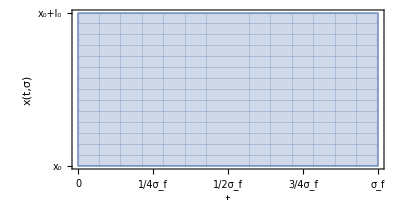

```mathematica
ParametricPlot[{τ,xF[τ,σ]/.HQFSol},Mnum[[1]],Mnum[[2]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13]},FrameTicks->{{{{AnalyticHQF[0,0][[2]],"x_0"},{AnalyticHQF[0,Subscript[σ, f]][[2]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}]
```

#### Spacetime

```mathematica
Xads={t[τ,σ], r[τ,σ],xI[τ,σ]};
adsMet = metric[Xads[[2]]];
AdsEom=EquationsOfMotion[eta,adsMet,psCords,Xads];
Print[AdsEom//MatrixForm];
```

(0.-2.48365 t^(0,2)[τ,σ]-(4.96729 r[τ,σ] (1. r^(0,1)[τ,σ] t^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] t^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)+(0.805267 r[τ,σ]^3 (1. r^(0,1)[τ,σ] t^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] t^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)+r[τ,σ]^2 (0.402634 t^(0,2)[τ,σ]-0.402634 t^(2,0)[τ,σ])+2.48365 t^(2,0)[τ,σ]
0.-(0.251646 r^(0,2)[τ,σ])/(-6.1685+r[τ,σ]^2)-(0.402634 r[τ,σ]^3 (1. (t^(0,1)[τ,σ])^2-1. (t^(1,0)[τ,σ])^2))/(-6.1685+r[τ,σ]^2)+r[τ,σ] ((0.251646 (r^(0,1)[τ,σ])^2)/((-6.1685+r[τ,σ]^2)^2)+(2.48365 (t^(0,1)[τ,σ])^2)/(-6.1685+r[τ,σ]^2)+0.402634 (xI^(0,1)[τ,σ])^2-(0.251646 (r^(1,0)[τ,σ])^2)/((-6.1685+r[τ,σ]^2)^2)-(2.48365 (t^(1,0)[τ,σ])^2)/(-6.1685+r[τ,σ]^2)-0.402634 (xI^(1,0)[τ,σ])^2)+(0.251646 r^(2,0)[τ,σ])/(-6.1685+r[τ,σ]^2)
0.+(4.96729 r[τ,σ] (1. r^(0,1)[τ,σ] xI^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] xI^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)-(0.805267 r[τ,σ]^3 (1. r^(0,1)[τ,σ] xI^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] xI^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)+r[τ,σ]^2 (-0.402634 xI^(0,2)[τ,σ]+0.402634 xI^(2,0)[τ,σ]))

```mathematica
AdsEom = AdsEom /. t-> Function[{τ,σ}, τ] //Simplify;(*Static time gauge condition*)
Print[AdsEom//MatrixForm];
```

(0.+(4.96729 r[τ,σ] r^(1,0)[τ,σ])/(-6.1685+r[τ,σ]^2)-(0.805267 r[τ,σ]^3 r^(1,0)[τ,σ])/(-6.1685+r[τ,σ]^2)
0.+(0.402634 r[τ,σ]^3)/(-6.1685+r[τ,σ]^2)-(0.251646 r^(0,2)[τ,σ])/(-6.1685+r[τ,σ]^2)+r[τ,σ] (-2.48365/(-6.1685+r[τ,σ]^2)+(0.251646 (r^(0,1)[τ,σ])^2)/((-6.1685+r[τ,σ]^2)^2)+0.402634 (xI^(0,1)[τ,σ])^2-(0.251646 (r^(1,0)[τ,σ])^2)/((-6.1685+r[τ,σ]^2)^2)-0.402634 (xI^(1,0)[τ,σ])^2)+(0.251646 r^(2,0)[τ,σ])/(-6.1685+r[τ,σ]^2)
0.+(4.96729 r[τ,σ] (1. r^(0,1)[τ,σ] xI^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] xI^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)-(0.805267 r[τ,σ]^3 (1. r^(0,1)[τ,σ] xI^(0,1)[τ,σ]-1. r^(1,0)[τ,σ] xI^(1,0)[τ,σ]))/(-6.1685+r[τ,σ]^2)+r[τ,σ]^2 (-0.402634 xI^(0,2)[τ,σ]+0.402634 xI^(2,0)[τ,σ]))

```mathematica
BndIntConditionsHQadsR:= {
r[0,σ] == rAdsHQ[σ],Derivative[1,0][r][0,σ]==0 ,(*Initial Condition*)
r[τ,0]==rAdsHQ[0] ,r[τ,Subscript[σ, f]]==rAdsHQ[Subscript[σ, f]](*Spacial Boundary Condition*)
 };
BndIntConditionsHQadsX:= {
xI[0,σ] == 0,Derivative[1,0][xI][0,σ]==0 ,(*Initial Condition*)
xI[τ,0]==0 (*Spacial Boundary Condition*)
 };
```

```mathematica
HQadsSol = NDSolve[Flatten[{AdsEom[[2]]==0,AdsEom[[3]]==NeumannValue[0,σ==Subscript[σ, f]],BndIntConditionsHQadsR,BndIntConditionsHQadsX}],{r[τ,σ],xI[τ,σ]} ,Mnum[[1]],Mnum[[2]]];
```

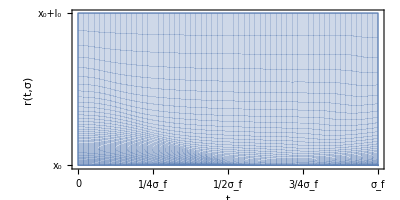

-Graphics3D-

-Graphics3D-

```mathematica
ParametricPlot[{τ,r[τ,σ]}/.HQadsSol, Mnum[[1]],Mnum[[2]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13]},FrameTicks->{{{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}]
ParametricPlot3D[{τ,r[τ,σ],xI[τ,σ]}/.HQadsSol, Mnum[[1]],Mnum[[2]],AspectRatio->1/4,AxesLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13],Style["x(t,σ)",Bold,13]},PlotRange->{Full,Full,{-0.2,0.2}},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}},{{0,0}}}, Mesh->15]
Plot3D[r[τ,σ]/.HQadsSol,Mnum[[1]],Mnum[[2]],AxesLabel->{Style[t,Bold,13] ,Style[σ,Bold,13],Style["r(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsHQ[0],"x_0"},{rAdsHQ[Subscript[σ, f]],"x_0+l_0"}}}]
```

### Light Quark

#### Flat Spacetime

```mathematica
BndIntConditionsLQF:= {
xF[0,σ] == AnalyticLQF[0,σ,Subscript[σ, f]][[2]],Derivative[1,0][xF][0,σ]==0 ,(*Initial Condition*)
xF[τ,0]==AnalyticLQF[0,0,Subscript[σ, f]][[2]] (*Spacial Boundary Condition*)
 };
```

```mathematica
LQFSol = NumericSolve[{FlatEom[[2]]==NeumannValue[0,σ==Subscript[σ, f]],BndIntConditionsLQF},xF[τ,σ],Mnum];
```

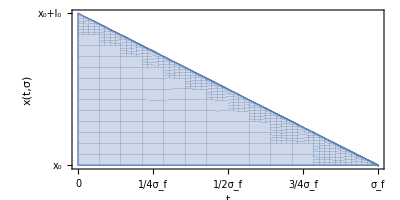

```mathematica
ParametricPlot[{τ,xF[τ,σ]/.LQFSol},Mnum[[1]],Mnum[[2]], AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["x(t,σ)",Bold,13]},FrameTicks->{{{{AnalyticLQF[0,0,Subscript[σ, f]][[2]],"x_0"},{AnalyticLQF[0,Subscript[σ, f],Subscript[σ, f]][[2]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}]
```

#### Spacetime

```mathematica
BndIntConditionsLQadsR:= {
r[0,σ] == rAdsLQ[0,σ,Subscript[σ, f]],Derivative[1,0][r][0,σ]==0 ,(*Initial Condition*)
r[τ,0]==rAdsLQ[τ,0,Subscript[σ, f]] (*Spacial Boundary Condition*)
 };
BndIntConditionsLQadsX:= {
xI[0,σ] == 0,Derivative[1,0][xI][0,σ]==0 ,(*Initial Condition*)
xI[τ,0]==0 (*Spacial Boundary Condition*)
 };
```

```mathematica
LQadsSol = NumericSolve[{AdsEom[[2]]==NeumannValue[0,σ==Subscript[σ, f]],AdsEom[[3]]==NeumannValue[0,σ==Subscript[σ, f]],BndIntConditionsLQadsR,BndIntConditionsLQadsX},{r[τ,σ],xI[τ,σ]} ,Mnum];
```

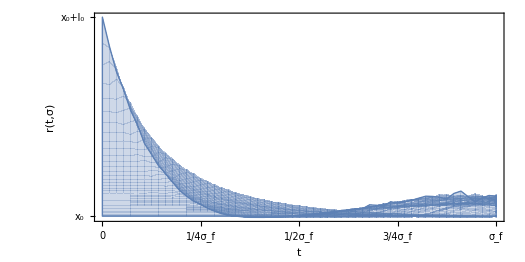

-Graphics3D-

-Graphics3D-

```mathematica
ParametricPlot[{τ,r[τ,σ]}/.LQadsSol, Mnum[[1]],Mnum[[2]],AspectRatio->1/2,FrameLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13]},FrameTicks->{{{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}},None},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}, PlotRange-> All (*{{Subscript[σ, f]/5,3Subscript[σ, f]/5},{rAdsLQ[0,0,Subscript[σ, f]]-0.2,rAdsLQ[0,0,Subscript[σ, f]]+0.5}}*)] (*Replace the `All' after PlotRange with the commented code to reproduce figure 15*)
ParametricPlot3D[{τ,r[τ,σ],xI[τ,σ]}/.LQadsSol, Mnum[[1]],Mnum[[2]],AspectRatio->1/4,AxesLabel->{Style[t,Bold,13] ,Style["r(t,σ)",Bold,13],Style["x(t,σ)",Bold,13]},PlotRange->{Full,Full,{-0.2,0.2}},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}},{{0,0}}}, ViewPoint->{2,1,0}]
Plot3D[r[τ,σ]/.LQadsSol,Mnum[[1]],Mnum[[2]],AxesLabel->{Style[t,Bold,13] ,Style[σ,Bold,13],Style["r(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{rAdsLQ[0,0,Subscript[σ, f]],"x_0"},{rAdsLQ[0,Subscript[σ, f],Subscript[σ, f]],"x_0+l_0"}}}, PlotRange->All, ViewPoint->{2,-2,1}]
```

### Comparison plots

Plot of the difference between the numeric and analytic results in each case (comparing only the radial coordinate for the  cases as the transverse direction is trivial).

Heavy Quark flat spacetime:

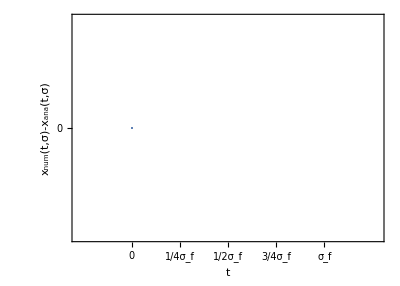

```mathematica
ParametricPlot[{τ,xF[τ,σ]/. HQFSol}-AnalyticHQF[τ,σ],Mnum[[1]],Mnum[[2]],FrameLabel->{Style[t,Bold,13] ,Style["x_num(t,σ)-x_ana(t,σ)",Bold,13]},FrameTicks->{{{0,0}},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}, PlotRange->{{-0.2,Subscript[σ, f]+0.2},{-0.4,0.4}}]
```

Heavy Quark :

```mathematica
Plot3D[(r[τ,σ]/.HQadsSol)-rAdsHQ[σ], Mnum[[1]],Mnum[[2]],AspectRatio->1/2,AxesLabel->{Style[t,Bold,13] ,Style[σ,Bold,13],Style["r_num(t,σ)-r_ana(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{-rAdsHQ[Subscript[σ, f]]/10,"-l_0/10"},{0,0},{rAdsHQ[Subscript[σ, f]]/10,"l_0/10"}}}, PlotRange->{All,All,{-rAdsHQ[Subscript[σ, f]]/8,rAdsHQ[Subscript[σ, f]]/8}}]
```

-Graphics3D-

Light Quark flat spacetime:

```mathematica
ParametricPlot[{τ,xF[τ,σ]/. LQFSol}-AnalyticLQF[τ,σ,Subscript[σ, f]],Mnum[[1]],Mnum[[2]],FrameLabel->{Style[t,Bold,13] ,Style["x_num(t,σ)-x_ana(t,σ)",Bold,13]},FrameTicks->{{{0,0}},{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},None}}, PlotRange->{{-0.2,Subscript[σ, f]+0.2},{-0.4,0.4}}]
```

-Graphics-

```mathematica
Subscript[s, f]=Subscript[σ, f] ; (*Mathematica has problems handling having both σ and Subscript[σ, f] in the same plotting command; I don't know why it was only a problem for this plot.*)
```

Light Quark :

```mathematica
Plot3D[(r[τ,σ]/. LQadsSol)-rAdsLQ[τ,σ,Subscript[s, f]],Mnum[[1]],Mnum[[2]],AxesLabel->{Style[t,Bold,13] ,Style[σ,Bold,13],Style["r_num(t,σ)-r_ana(t,σ)",Bold,13]},Ticks->{{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{0,0} ,{Subscript[σ, f]/4,"1/4σ_f"},{2 Subscript[σ, f]/4,"1/2σ_f"}, {3 Subscript[σ, f]/4,"3/4σ_f"},{Subscript[σ, f],"σ_f"}},{{-rAdsHQ[Subscript[σ, f]]/10,"-l_0/10"},{0,0},{rAdsHQ[Subscript[σ, f]]/10,"l_0/10"}}}, PlotRange->{All,All,{-rAdsHQ[Subscript[σ, f]]/8,rAdsHQ[Subscript[σ, f]]/8}}]
```